```mathematica
SetDirectory[NotebookDirectory[]];
Import["init.wl"];
```

In order to solve a quantum mechanical problem by numerical methods, we need to be able to represent the Hamiltonian of the system in way in which the computer can understand.  This is typically done by representing the Hamiltonian operator in a finite polynomial basis.
In the examples given here, we use the Tchebychev polynomials as our basis.  As it turns out, the Tchebychev sine functions coincide with the particle in a box states.  This particular representation is fairly generic and can be used to solve a wide range of problems. 
Other polynomial representations, for example, the Gauss Hermite polynomials or Laguerre polynomials, corresponding to the Harmonic Oscillator and radial  Hydrogen-like atom functions respectively, are useful in more specific situations.

The module tcheby[npts, xmin, xmax]  returns a set of points, a transformation matrix, and the eigenstates the Laplacian operator, ((-∂^2)/(∂x^2)),  in the basis, and a set of weights. 
The transformation matrix carries one from the finite basis representation (FBR) to a discrete variable representation (DVR).

⟨ x_i| ψ ⟩ = ∑_(n=1)^N ⟨x_i|n⟩ ⟨n|ψ⟩ = ∑_(n=1)^N T_(i n) ⟨n|ψ⟩

This relation is invertible, allowing us to interconvert the wavefunction or operators back and forth between the two representations. 
Notice there is a one-to-one correspondence between number of points x_i and total number of basis functions.   Consequently, representing the problem on a point-wise grid or a finite basis is equivalent.
In fact, what we do is take advantage of this one-to-one relationship to transform parts of the Hamiltonian from one representation to another and assemble the total Hamiltonian in either the DVR or the FBR depending upon which is more sparse.  Typically, one picks a DVR/FBR combination so that the kinetic energy part of the Hamiltonian is diagonal in the basis representation.  Scalar potentials, i.e. potentials which can be represented as a function of coordinates, are automatically diagonal in the DVR.   

For more detailed information regarding DVRs and their usage, refer to  ,

J. C. Light, I. P. Hamilton, and J. V. Lill, J. Chem. Phys 82, 1400 (1985).

```mathematica
tcheby[npts_Integer,xmin_,xmax_]:=Module[
{del,pts,t,fbrke,w},
del=xmax-xmin;
pts=N[Table[(i del)/(npts+1)+xmin,{i,npts}]];
t=N[Table[√(2./(npts+1)) Sin[((i j) π)/(npts+1)],{i,npts},{j,npts}]];
fbrke=N[Table[((i π)/del)^2,{i,npts}]];
w=N[Table[del/(npts+1),{i,npts}]];
Return[{pts,t,fbrke,w}]]
dv2fb[dvr_,t_]:=t.dvr.Transpose[t];
fb2dv[fbr_,t_]:=Transpose[t].fbr.t;
```

### Bound States of the Morse Well

Here we will solve for the bound states of the Morse oscillator well.  We will use a 100 point basis ranging from [-3,32]. 
We first construct the Hamiltonian matrix, hdvr, in the DVR basis and then diagonalize it to determine the  eigenvalues and eigenvectors.

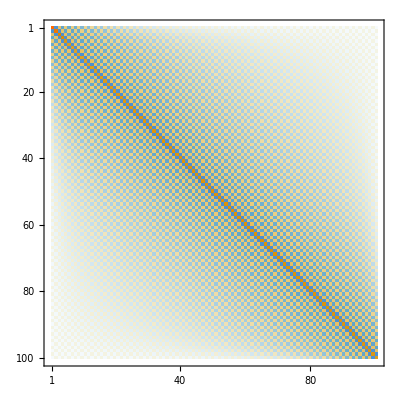

```mathematica
npts = 100 ; 
xmin = -3.0;
xmax = +32.0;
de = 3.0;
a = .5 ; 
m = 1.0; 
ℏ  = 1.0; 
{pts,t,fbrke,w} = tcheby[npts,xmin,xmax];
v[x_]:= de (1-Exp[-a x])^2-de;
vdvr = v[pts]//Thread;
fbrke = fbrke * ℏ^2/(2m);
hdvr =  fb2dv[DiagonalMatrix[fbrke],t] + DiagonalMatrix[vdvr];
MatrixPlot[ hdvr]
```

Notice here we construct the DVR Hamiltonian by constructing a diagonal matrix of the potential evaluated over the DVR points. To this we add the kinetic energy contribution by transforming the diagonal fbrke matrix from the basis representation to the DVR. 

It’s always useful to plot the potential surface just to make sure we have the relevant range covered by the DVR points.

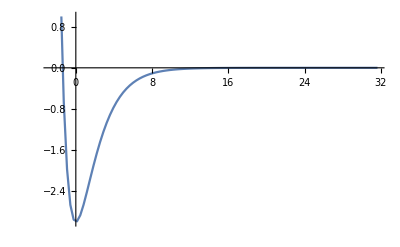

```mathematica
plotV=ListPlot[
Transpose[{pts,vdvr}],PlotRange->{-3,1},Joined->True,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["V",FontSize->20]},PlotLabel->MaTeX["\\text{Potential Energy Surface}",FontSize->20]
]
```

Solve for the eigenvalues/eigenvectors,

```mathematica
{ω,ϕ}=Transpose[Sort[Transpose[Eigensystem[hdvr]]]];
TableForm[Take[ω,10]]
```

-2.41888
-1.44413
-0.719388
-0.244643
-0.0198923
0.0113421
0.0400867
0.0823905
0.136925
0.202919

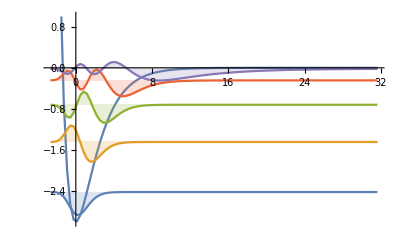

```mathematica
plotWF = ListPlot[Table[Transpose[{pts,ω[[i]]+ϕ[[i]]}],{i,1,5}],PlotRange->{{-3,32},{-3,1}},Joined->True,
Filling->Table[i->ω[[i]],{i,1,5}]];
Show[plotV,plotWF]
```

Notice that the highest bound state is very extended in x.

### Tunneling Splitting in the Double Well Potential

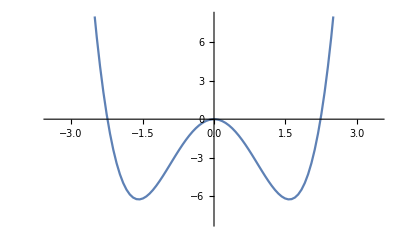

```mathematica
{pts2,t2,fbrke2,w2}=tcheby[100,-3.5,3.5];
v2[x_]:=-5 x^2+x^4;
v2dvr=Thread@v2[pts2];
m=1.0;
plotV2=ListPlot[
Transpose[{pts2,v2dvr}],PlotRange->{-8,8},Joined->True,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["V",FontSize->20]},PlotLabel->MaTeX["\\text{Potential Energy Surface}",FontSize->20]
]
```

```mathematica
fbrke2=fbrke2/(2 m);h2dvr=fb2dv[DiagonalMatrix[fbrke2],t2]+DiagonalMatrix[v2dvr];{ω,ψ}=Transpose[Sort[Transpose[Eigensystem[h2dvr]]]];
```

```mathematica
TableForm[Take[ω,10]]
```

-4.13576
-4.11911
-0.756761
-0.210676
1.92129
3.8373
6.18057
8.7403
11.5102
14.4645

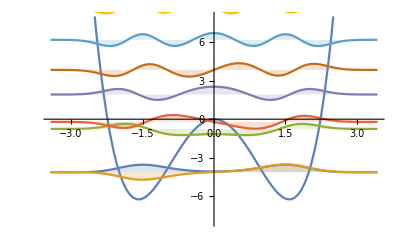

```mathematica
nn = 10;
amp = 3.0;
plotWF2 = ListPlot[Table[Transpose[{pts2,ω[[i]]+amp*ψ[[i]]}],{i,1,nn}],Joined->True,
Filling->Table[i->ω[[i]],{i,1,nn}]];
Show[plotV2,plotWF2]
```

Convergence with respect to number of points/basis functions,

```mathematica
evalues  = {};
tt             = {};
npts         = {};
Do[
{pts2,t2,fbrke2,w2}=tcheby[nn,-3.5,3.5];
v2dvr=Thread@v2[pts2];
fbrke2=fbrke2/(2 m);
h2dvr=fb2dv[DiagonalMatrix[fbrke2],t2]+DiagonalMatrix[v2dvr];
{t,ω}=Timing[Sort[Eigenvalues[h2dvr]]];
tt = Append[tt,t]/.Second-> 1;
npts = Append[npts,nn];
evalues = Append[evalues,Take[ω,5]],{nn,5,200,1}
]
```

```mathematica
data=FindClusters[Transpose[{npts,tt}]];
```

```mathematica
ff=Fit[data[[2]],{1,x^2,x^4},x]
```

0.00453868-1.06439×10^-7 x^2+3.91557×10^-12 x^4

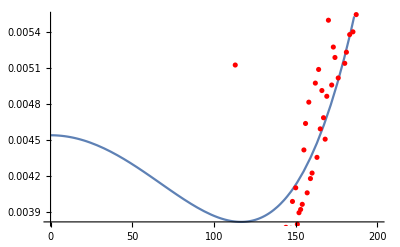

```mathematica
p1=ListPlot[Transpose[{npts,tt}],Joined->False,PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
p2=Plot[ff,{x,0,200},AxesLabel->{MaTeX["N",FontSize->20],MaTeX["\\text{timing (s)}",FontSize->20]}];
Show[p2,p1,DisplayFunction->$DisplayFunction]
```

```mathematica
TableForm@Transpose@evalues
```

-3.99503 | -4.86422 | -4.41314 | -3.93539 | -4.12221 | -4.20143 | -4.14945 | -4.12796 | -4.13371 | -4.13695 | -4.13623 | -4.13573 | -4.13572 | -4.13576 | -4.13577 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576 | -4.13576
-3.89516 | -4.80376 | -4.41142 | -3.90474 | -4.1146 | -4.18375 | -4.13352 | -4.11079 | -4.11721 | -4.12028 | -4.1196 | -4.11907 | -4.11906 | -4.11911 | -4.11912 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911 | -4.11911
1.32273 | -0.42403 | -1.30405 | -1.30007 | -0.478761 | -0.74946 | -0.854 | -0.781931 | -0.744169 | -0.75379 | -0.758615 | -0.757548 | -0.756701 | -0.756688 | -0.756756 | -0.756767 | -0.756762 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761 | -0.756761
3.47605 | 1.58785 | -1.00884 | -1.06989 | 0.198239 | -0.0907741 | -0.377946 | -0.273471 | -0.192238 | -0.202051 | -0.21366 | -0.212381 | -0.210678 | -0.210524 | -0.210659 | -0.210686 | -0.21068 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676 | -0.210676
3.56411 | 9.25061 | 3.08347 | 0.99913 | 1.43909 | 2.44294 | 1.87875 | 1.72988 | 1.89681 | 1.94603 | 1.92426 | 1.91714 | 1.92018 | 1.9215 | 1.92142 | 1.92129 | 1.92128 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129 | 1.92129

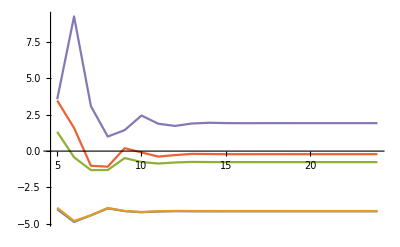

```mathematica
ListPlot[Transpose@Table[Table[{npts[[i]],evalues[[i,j]]},{j,5}],{i,20}],Joined->True,AxesLabel->{MaTeX["N",FontSize->20],MaTeX["\\text{Eigen Values}",FontSize->20]}]
```